```mathematica
Clear[ndf,pdf,cdf]
ndf[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
(*cdf=Function[{θ,α},Evaluate[Integrate[2*π*ndf[θ,α]*Cos[θ]*Sin[θ],θ]]]*)
cdf[θ_,α_]:=(1-Cos[θ]^2)/(1+Cos[θ]^2*(α^2-1))
pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
pdfCos[cosθ_,α_]:=α^2/(π*(cosθ^2*(α^2-1)+1)^2)*cosθ
```

Compute the difference of the PDFs of 2 neighbor pixels

```mathematica
(*Clear[α]
Integrate[2*π*(ndf[θ,α] - ndf[θ-β,α])*Cos[θ]*Sin[θ],θ]*)
```

```mathematica
ndf2[μ_,α_]:=α^2/(π*(μ^2*(α^2-1)+1)^2)
test[μ0_,α_]:=cdf[μ0,α]+ NIntegrate[2*π*(ndf2[μ,α] - ndf2[μ-μ0,α])*μ*√(1-μ^2),{μ,μ0,0}]
```

```mathematica
Manipulate[Plot[{test[μ0,α],cdf[μ0,α]},{α,0,1},PlotRange->{0,1}],{μ0,1,0}]
```

```mathematica
test[θ0_,α_]:=cdf[Cos[θ0],α]+ NIntegrate[2*π*(ndf[θ,α] - ndf[θ-θ0,α])*Cos[θ]*Sin[θ],{θ,θ0,π/2}]
Manipulate[Plot[{test[θ,α],cdf[Cos[θ],α]},{α,0,1},PlotRange->{-1,1}],{θ,0.01,π/2}]
```

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

Test with subtraction of the 2 lobes:

```mathematica
Manipulate[Show[Plot[(pdf[θ,α]*Sin[θ])/cdf[θ0/2,α]-(pdf[θ0-θ,α]*Sin[θ0-θ])/cdf[θ0/2,α],{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

Test with multiplication of the 2 lobes (true correlation):

```mathematica
Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

Showing angular correlation visually:

```mathematica
ColorData[97,"ColorList"]
ColorData[97][1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
defaultBlue=ColorData[97][1];
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]}, 4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],α]/cdf[θ0/2,α]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],α]/cdf[θ0/2,α]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],α]*pdf[Abs[(π/4+θ0/2)-θ],α])/cdf[θ0/2,α]^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ],{θ,0,π/2},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
```

```mathematica
(*Clear[α]
Integrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,θ]*)
```

```mathematica
(*Manipulate[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[NIntegrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
(*Manipulate[Plot[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]*)
Manipulate[Plot[NIntegrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]
```

NIntegrate::inumr: The integrand α^4\ (1 + (5/8 + √5/8)\ (-1 + α^2))^2\ Cos[π/10 - θ]\ Cos[θ]\ Sin[π/10 - θ]\ Sin[θ]/(3/8 - √5/8)^2\ π^2\ (1 + (-1 + α^2)\ Cos[Times[« 2 »] + Times[« 2 »]]^2)^2\ (1 + (-1 + α^2)\ Cos[θ]^2)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.314159, -0.15708}}.

Show the correlation

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ]*ndf[θ-θ0,α]*Cos[θ-θ0],{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,0.05},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
(*Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/π)^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[Show[Plot[(pdf[θ,α]*pdf[θ0-θ,α])/cdf[θ0/2,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,((√2)/π)^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((ndf(θ_0/2,α) cos(θ_0/2)sin(θ_0/2))/(cdf(θ_0/2,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (ndf(π/4,1) cos(π/4)sin(π/4))/(cdf(π/2,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/π

```mathematica
(ndf[π/4,1]*Cos[π/4]*Sin[π/4])/cdf[π/4,1]
pdf[π/4,1]/cdf[π/4,1]
```

1/π

(√2)/π

```mathematica
Solve[(pdf[θ,α]*Sin[θ])/cdf[θ,α]==c,α]
```

{{α→-(ⅈ √c √π (-1+Cos[θ]^2))/(√(c π Cos[θ]^2-c π Cos[θ]^4-Cos[θ] Sin[θ]))},{α→(ⅈ √c √π (-1+Cos[θ]^2))/(√(c π Cos[θ]^2-c π Cos[θ]^4-Cos[θ] Sin[θ]))}}

```mathematica
Clear[c]
Solve[pdf[θ,α]/cdf[θ,α]==c,α]
```

{{α→-(ⅈ √c √π (-1+Cos[θ]^2))/(√(-Cos[θ]+c π Cos[θ]^2-c π Cos[θ]^4))},{α→(ⅈ √c √π (-1+Cos[θ]^2))/(√(-Cos[θ]+c π Cos[θ]^2-c π Cos[θ]^4))}}

```mathematica
(*cmax = 1/π;
c=cmax/(8π);
sqAlpha[θ_]:=(c*Cos[θ]^2)/(Sin[θ]-c*Sin[θ]^2)
sqAlpha[θ_]:=(-π*cmax* Sin[θ]^4)/(π*cmax* Cos[θ]^2-π*cmax* Cos[θ]^4-Cos[θ]*Sin[θ])*)
```

```mathematica
cmax=(√2)/π;
c=cmax * π;
(*sqAlpha[θ_]:=(-c*Sin[θ]^4)/(c* Cos[θ]^2-c* Cos[θ]^4-Cos[θ]*Sin[θ]) with sin(θ) *)
sqAlpha[θ_]:=(-c*Sin[θ]^4)/(c* Cos[θ]^2-c* Cos[θ]^4-Cos[θ])
```

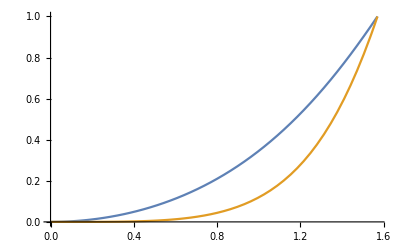

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
```

```mathematica
mipMax=8;
(*mu[mip_]:=1-1/3 2^(2(mip-mipMax))   Solid angles yields θ > π/2*)
mu[mip_]:=1/(√(1+2^(2(mip-mipMax))))
sqRoughnessFromMip[mip_]:=sqAlpha[ ArcCos[mu[mip]] ]

mu[8]
2*ArcCos[mu[8]]
Table[N[sqRoughnessFromMip[mip]],{mip,0,mipMax}]
```

1/(√2)

π/2

{3.29272×10^-10,5.26833×10^-9,8.42919×10^-8,1.34859×10^-6,0.0000215718,0.000344773,0.0054869,0.0846641,1.}

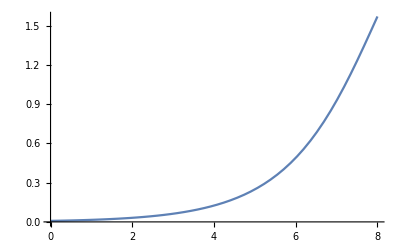

```mathematica
Plot[2*ArcCos[mu[mip]],{mip,0,mipMax},PlotRange->{0,π/2}]
```

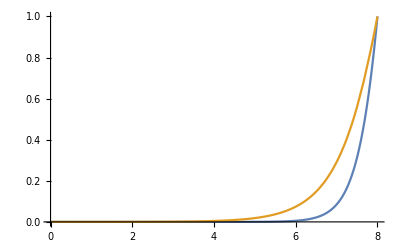

```mathematica
Plot[{sqRoughnessFromMip[mip],√sqRoughnessFromMip[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

It would look like we’re doing the same thing all over again but the normalization by pdf(0,α) makes much more sense than dividing by the cdf!

Showing angular correlation visually:

```mathematica
defaultBlue=ColorData[97][1];
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],α]/pdf[0,α]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],α]/pdf[0,α]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],α]*pdf[Abs[(π/4+θ0/2)-θ],α])/pdf[0,α]^2*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

Plotting angular correlation as a function of angle:

```mathematica
(*Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/pdf[0,α]^2,{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[Show[Plot[(pdf[θ,α]*pdf[θ0-θ,α])/pdf[0,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/(√2))^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((pdf(θ_0/2,α))/(pdf(0,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (pdf(π/4,1))/(pdf(0,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/(√2)

```mathematica
(ndf[π/4,1]*Cos[π/4])/pdf[0,1]
pdf[π/4,1]/pdf[0,1]
```

1/(√2)

1/(√2)

```mathematica
Clear[c,θ,α]
(*Solve[pdf[θ,α]/pdf[0,α]==c,α]*)
Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,α]
```

{{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))}}

```mathematica
Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,b]
```

{{b→1/2 √(-(2 √2)/(-√2+2 √2 α^2-√2 α^4)+16+(16 2^1 α^12)/(3 (1) 1)+(1)^(1/3)/(3 2^(1/3) (1-4 α^2+6 α^4-4 α^6+α^8)))-1/2 √1},{b→1},1,{b→-1/2 √1+1}}
 |  |  |  |

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
```

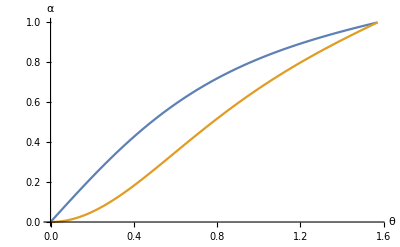

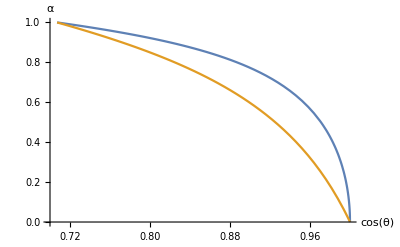

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqAlphaMu[μ],sqAlphaMu[μ]},{μ,1/(√2),1},PlotRange->{{0.70,1},{0,1}},AxesLabel->{"cos(θ)","α"}]
```

2/3

1.68214

{0.00733224,0.0146636,0.0293201,0.0585836,0.116718,0.229944,0.434916,0.731737,1.02718}

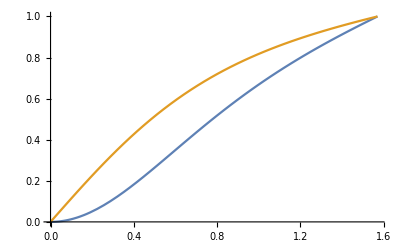

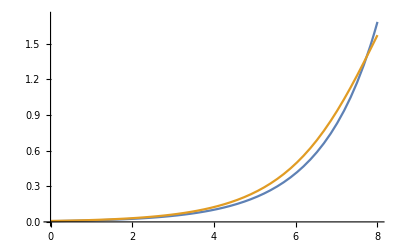

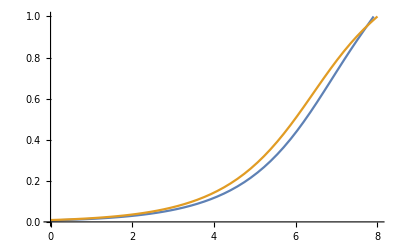

```mathematica
mipMax=8;
mu[mip_]:=1-1/3 2^(2(mip-mipMax))   (*Solid angles yields θ > π/2*)
mu2[mip_]:=1/(√(1+2^(2(mip-mipMax))))
sqRoughnessFromMip[mip_]:=sqAlpha[ArcCos[mu[mip]] ]
sqRoughnessFromMip2[mip_]:=sqAlpha[ArcCos[mu2[mip]] ]
mu[8]
N[2*ArcCos[mu[8]]]
Table[N[√sqRoughnessFromMip[mip]],{mip,0,mipMax}]
Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
Plot[{2*ArcCos[mu[mip]],2*ArcCos[mu2[mip]]},{mip,0,mipMax},PlotRange->{0,1.1*π/2}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip2[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

```mathematica
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]*pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]])/pdf[0,√sqAlpha[θ0/2]]^2*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{θ0,π/2},0.001,π/2}]
```

Fitting

The expression to get μ from roughness is a nightmare to invert so let’s do a curve fitting instead...

{{1.,0.707107},{0.995845,0.710036},{0.991663,0.712965},{0.987454,0.715894},{0.983216,0.718823},{0.978948,0.721751},{0.97465,0.72468},{0.970321,0.727609},{0.965958,0.730538},{0.961562,0.733467},{0.957132,0.736396},{0.952665,0.739325},{0.948161,0.742254},{0.943619,0.745183},{0.939037,0.748112},{0.934415,0.751041},{0.92975,0.75397},{0.925042,0.756899},{0.920289,0.759828},{0.915489,0.762756},{0.910642,0.765685},{0.905746,0.768614},{0.900799,0.771543},{0.895799,0.774472},{0.890746,0.777401},{0.885636,0.78033},{0.880469,0.783259},{0.875243,0.786188},{0.869956,0.789117},{0.864605,0.792046},{0.859189,0.794975},{0.853706,0.797904},{0.848154,0.800833},{0.84253,0.803762},{0.836832,0.80669},{0.831058,0.809619},{0.825206,0.812548},{0.819272,0.815477},{0.813254,0.818406},{0.80715,0.821335},{0.800956,0.824264},{0.794669,0.827193},{0.788287,0.830122},{0.781806,0.833051},{0.775224,0.83598},{0.768535,0.838909},{0.761738,0.841838},{0.754828,0.844767},{0.747801,0.847696},{0.740653,0.850624},{0.73338,0.853553},{0.725978,0.856482},{0.718442,0.859411},{0.710767,0.86234},{0.702948,0.865269},{0.694979,0.868198},{0.686856,0.871127},{0.678573,0.874056},{0.670123,0.876985},{0.6615,0.879914},{0.652698,0.882843},{0.64371,0.885772},{0.634528,0.888701},{0.625144,0.89163},{0.615552,0.894558},{0.605741,0.897487},{0.595704,0.900416},{0.58543,0.903345},{0.574911,0.906274},{0.564135,0.909203},{0.553092,0.912132},{0.541769,0.915061},{0.530155,0.91799},{0.518237,0.920919},{0.506001,0.923848},{0.493432,0.926777},{0.480515,0.929706},{0.467234,0.932635},{0.45357,0.935563},{0.439506,0.938492},{0.425022,0.941421},{0.410097,0.94435},{0.394707,0.947279},{0.37883,0.950208},{0.36244,0.953137},{0.345509,0.956066},{0.328008,0.958995},{0.309905,0.961924},{0.291167,0.964853},{0.271756,0.967782},{0.251635,0.970711},{0.23076,0.97364},{0.209086,0.976569},{0.186564,0.979497},{0.163139,0.982426},{0.138754,0.985355},{0.113346,0.988284},{0.0868448,0.991213},{0.0591763,0.994142},{0.030258,0.997071},{0.,1.}}

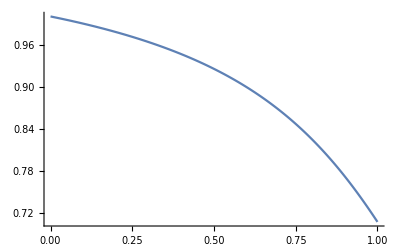

```mathematica
data=Table[{ N[sqAlphaMu[μ]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}]
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(1.2547-1.87042 x+0.720235 x^2)/(1.2547-1.75224 x+0.645329 x^2)]

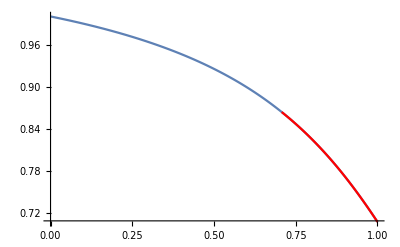

1.00011

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)

f=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f[x],{x,1/(√2),1},PlotStyle->Red]]
√2 f[1]
```

3D Lobes Inter-Penetration Modeling

Here we’re attempting to port the same reflection to the 3D realm. The idea is measuring how much 2 adjacent lobes interpenetrate each other depending on the separation angle (i.e. the lobe’s aperture angle) and the roughness of the lobe.
Once again we “normalize a lobe” by dividing by its largest amplitude at θ=0 and we’re looking to compute the integral:

	I=∫_-θ_0^θ_0 ∫_0^(π/2) (D(θ,α) D( θ', α ) cos(θ)  cos(θ') sin(θ))/(D( 0, α ))^2 ⅆθⅆϕ

Here, cos(θ')= sin( θ ) cos( ϕ ) sin( θ_0) + cos( θ ) cos( θ_0 ) and θ_0 is the cone’s aperture angle.

```mathematica
cosAngleChange[θ_,ϕ_,γ_]:=Sin[θ]*Cos[ϕ]*Sin[γ]+Cos[θ]*Cos[γ]
penelobe[θ_,ϕ_,γ_,α_]:=pdf[θ,α]*pdfCos[cosAngleChange[θ,ϕ,γ],α]
```

```mathematica
γ=0.1
α=0.05
NIntegrate[penelobe[θ,ϕ,γ,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}]
```

0.1

0.05

7.25895

1.0472

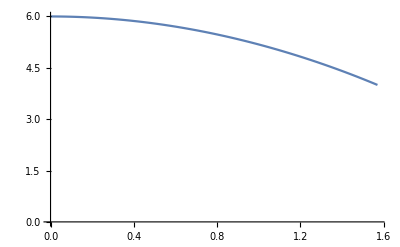

```mathematica
lobeSeparationAngle[θ0_]:=ArcCos[(Cos[θ0]-Cos[θ0]^2)/(1-Cos[θ0]^2)]
lobesCount[θ0_]:=(2π)/lobeSeparationAngle[θ0]
lobeSeparationAngle[0.0001]
Plot[lobesCount[θ0],{θ0,0,π/2},PlotRange->{0,6}]
```

Here it’s interesting to realize the limit converges to 6 possible neighbors, I would have expected an unlimited amount of neighbors as the lobes get thinner and thinner...
But after all, if you zoom in on things, even though they’re getting very small, maybe you always end up with 6 neighbor lobes no matter what.

The other extremity of 4 lobes when the angle is π/2is totally expected, on the other hand: each face of the cube has exactly 4 neighbor faces, thus 4 neighbor lobes.

```mathematica
Manipulate[lobesCount[θ0]*NIntegrate[penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

NIntegrate::inumr: The integrand 9.8696\ penelobe[θ, ϕ, 0.001, 1.]\ Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.5608}, {-1.5708, 1.5708}}.

```mathematica
Manipulate[NIntegrate[penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[lobesCount[θ0]*NIntegrate[penelobe[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.0001,1}]
```

```mathematica
Manipulate[NIntegrate[pdf[θ,α]/pdf[0,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[lobesCount[θ0]/2*NIntegrate[pdf[θ,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.0001,1}]
```

```mathematica
Manipulate[ParametricPlot3D[{
pdf[θ,α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]},
pdfCos[cosAngleChange[θ,ϕ,γ],α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]},
Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]}
},{θ,0,π/2},{ϕ,-π/2,π/2},PlotRange->{{0,0.5},{-0.25,0.25},{0,0.5}},AxesLabel->{"x","y","z"},PlotStyle->{Opacity[0.125],Opacity[0.125],Directive[Red,Opacity[1]]}],{{α,1},0.0001,1},{{γ,π/2},0.0001,π/2}]
```

```mathematica
penelobeMin[θ_,ϕ_,γ_,α_]:=Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]
Manipulate[NIntegrate[penelobeMin[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2},{ϕ,-π/2,π/2}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision],{{θ0,π/2},0.001,π/2},{{α,1},0.0001,1}]
```

```mathematica
SetDirectory["D:\\Workspaces\\Patapom.com\\Web\\blog\\patapom\\docs\\BRDF"]; 
countX=128;
countY=64;
```

```mathematica
ta=ParallelTable[{N[θ0],N[α],
NIntegrate[penelobeMin[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2},{ϕ,-π/2,π/2}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision]
}
,{θ0,0,π/2,(π/2)/countX}
,{α,0.001,1,(1-0.001)/countY}]
Export["VolumeInterPenetration_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv",ta,"CSV"];
```

{{{0.,0.001,0.500004888822118},{0.,0.25075,0.499957696132332},{0.,0.5005,0.501549446152682},{0.,0.75025,0.49999922390194},{0.,1.,0.5000008023512}},{{0.392699,0.001,0.0000111574662157308},{0.392699,0.25075,0.305366885191484},{0.392699,0.5005,0.449648629852615},{0.392699,0.75025,0.487795378277902},{0.392699,1.,0.495525191608768}},{{0.785398,0.001,2.64023019141407×10^-6},{0.785398,0.25075,0.128780405370246},{0.785398,0.5005,0.30799297858874},{0.785398,0.75025,0.416221488940014},{0.785398,1.,0.469395522472276}},{{1.1781,0.001,1.09265257039885×10^-6},{1.1781,0.25075,0.0617466500455922},{1.1781,0.5005,0.190239848322369},{1.1781,0.75025,0.313725303656169},{1.1781,1.,0.40813342366009}},{{1.5708,0.001,4.99011292696408×10^-7},{1.5708,0.25075,0.0299798103122976},{1.5708,0.5005,0.105595324195831},{1.5708,0.75025,0.200038195141229},{1.5708,1.,0.292971659095527}}}